## IFM Project

```mathematica
NotebookDirectory[]
```

C:\Users\User\Downloads\

### Initialization of the MZ operator

```mathematica
SimplifyFractionSeparate[expr_]:=Module[{num,denom,simpNum,simpDenom,result},{num,denom}=NumeratorDenominator[expr];(*Extract parts*)simpNum=Rationalize[FullSimplify[num]];(*Simplify numerator*)simpDenom=Rationalize[FullSimplify[denom]];(*Simplify denominator*)result=Simplify[simpNum/simpDenom];(*Final simplified result*)result]
```

```mathematica
$Pre=.;
$Post=.;
a =.;

$PrePrint=If[MatrixQ[#],MatrixForm[#],#]&
NumModes=3;
SetOptions[$FrontEnd,CommonDefaultFormatTypes->{"Output" ->StandardForm}]
OpVectorGenerator1[O_,NumModes]:=Table[{Subscript[O, q]},{q,1,NumModes} ];
ain = OpVectorGenerator1[a,NumModes]
(*BS is a beam splitter with the return and tra coefficients r,t*)
BS[r_,t_]:=({{r, t, 0}, {t, -r, 0}, {0, 0, 1}});
BS[√(1/2),√(1/2)].ain
(*P is a general phase object that gives a relative phase of φ to the first stage*) 
P[φ_]:=({{ⅇ^(ⅈ φ), 0, 0}, {0, 1, 0}, {0, 0, 1}});
(* Object is a general object stated in the lower MZ arm, it has an obseration probabilty of tO^2 and gives a phase of φO*)
Object[tO_,φO_]:=({{1, 0, 0}, {0, ⅇ^(ⅈ φO), 0}, {0, 0, 1}}).({{1, 0, 0}, {0, tO, √(1-tO^2)}, {0, √(1-tO^2), -tO}});
ObjectInv[tO_,φO_]:=({{1, 0, 0}, {0, tO, √(1-tO^2)}, {0, √(1-tO^2), -tO}}).({{1, 0, 0}, {0, ⅇ^(-ⅈ φO), 0}, {0, 0, 1}});
MZ[r_,t_,φ_,tO_,φO_]:=BS[r,t].Object[tO,φO].P[φ].BS[r,t];
Needs["Quantum`Notation`"];
SetQuantumAliases[];

For[k=0,k<NumModes+1,k++,DefineOperatorOnKets[Subscript[a, k],{|Subscript[w_, OverHat[Subscript[n, k]]]⟩:>Evaluate[√w|-1+Subscript[w, OverHat[Subscript[n, k]]]⟩⟨Subscript[w, OverHat[Subscript[n, k]]]|·|Subscript[w, OverHat[Subscript[n, k]]]⟩]}]];
For[k=0,k<NumModes+1,k++,DefineOperatorOnKets[SuperDagger[Subscript[a, k]],{|Subscript[w_, OverHat[Subscript[n, k]]]⟩:>Evaluate[√(w+1)|1+Subscript[w, OverHat[Subscript[n, k]]]⟩⟨Subscript[w, OverHat[Subscript[n, k]]]|·|Subscript[w, OverHat[Subscript[n, k]]]⟩]}]];
$Assumptions={1>=τ>=0 ,1>=t>=0 ,1>=r>=0 ,1>tO>0 ,1>R>0,1>T1>0,1>T2>0,1>T>0,1>r1>0,1>r>0,φ∈Reals,φO∈Reals,G∈Reals,tO∈Reals,θ∈Reals,m1∈Reals,m2∈Reals,m>0,m1>0,m2>0,R∈Reals,T∈Reals};
For[q=1,q<NumModes+1,q++,For[k=q,k<NumModes+1,k++,⟦Subscript[a, q],Subscript[a, k]⟧_-=0]];
For[q=1,q<NumModes+1,q++,For[k=q,k<NumModes+1,k++,⟦SuperDagger[Subscript[a, q]],SuperDagger[Subscript[a, k]]⟧_-=0]];
For[q=1,q<NumModes+1,q++,For[k=1,k<NumModes+1,k++,⟦Subscript[a, q],SuperDagger[Subscript[a, k]]⟧_-=KroneckerDelta[q-k]]];
For[q=1,q<NumModes+1,q++,For[k=1,k<NumModes+1,k++,⟦OverHat[Subscript[n, q]],SuperDagger[Subscript[a, k]]⟧_-=KroneckerDelta[q-k] SuperDagger[Subscript[a, k]]]];
For[q=1,q<NumModes+1,q++,For[k=1,k<NumModes+1,k++,⟦OverHat[Subscript[n, q]],Subscript[a, k]⟧_-=-KroneckerDelta[q-k] Subscript[a, k]]];
|vac⟩=⊗_(q=1)^NumModes|Subscript[0, OverHat[Subscript[n, q]]]⟩;

|Subscript[ψ, m1_,m2_]⟩:=|Subscript[m1, OverHat[Subscript[n, 1]]]⟩·|Subscript[m2, OverHat[Subscript[n, 2]]]⟩;//StandardForm;

(*Define 3 dimention state- 2 output and 1 observer*)
|Subscript[ψ, m1_,m2_,m3_]⟩:=|Subscript[m1, OverHat[Subscript[n, 1]]]⟩·|Subscript[m2, OverHat[Subscript[n, 2]]]⟩·|Subscript[m3, OverHat[Subscript[n, 3]]]⟩;//StandardForm;
```

If[MatrixQ[#1],#1,#1]&

(a_1
a_2
a_3)

(a_1/(√2)+a_2/(√2)
a_1/(√2)-a_2/(√2)
a_3)

#### function to calculate the probability to get out k,s for i,j in

```mathematica
ProbWithObject[i_,j_,k_,s_,R_,T_,φ_,tO_,φO_,m_]:=Module[{Cout,c,amp,prob},
Cout=MZ[√R,√T,φ,tO,φO].ain;
c[n_]:=Cout[[n,1]];
amp=⟨Subscript[ψ, 0,0,0]|·(√(1/(k!*s!*(m-s-k)!))c[1]^k·c[2]^s·c[3]^(m-s-k))·|Subscript[ψ, i,j,m-i-j]⟩;
prob=Simplify[ComplexExpand[Abs[amp]^2]];
prob//Simplify];
```

#### function to calculate all output probs for i,j in 2 photon

```mathematica
list2={{0,0},{1,0},{0,1},{2,0},{0,2},{1,1}};
```

all probs in asymmetric MZI with object

```mathematica
Probs2obas[pairsList_,i_,j_]:=Module[{allResults}, allResults=Association@Table[p->ProbWithObject[i,j,p[[1]],p[[2]],1-T,T,0,tO,φO,2],{p,pairsList}];
<|"All Results"->allResults|>//Dataset];
```

all probs in asymmetric MZI with out object

```mathematica
Probs2as[pairsList_,i_,j_]:=Module[{allResults}, allResults=Association@Table[p->ProbWithObject[i,j,p[[1]],p[[2]],1-T,T,0,1,0,2],{p,pairsList}];
<|"All Results"->allResults|>//Dataset];
```

all probs in symmetric MZI with object

```mathematica
Probs2obs[pairsList_,i_,j_]:=Module[{allResults}, allResults=Association@Table[p->ProbWithObject[i,j,p[[1]],p[[2]],1/2,1/2,π,tO,φO,2],{p,pairsList}];
<|"All Results"->allResults|>//Dataset];
```

all probs in asymmetric MZI with out object

```mathematica
Probs2s[pairsList_,i_,j_]:=Module[{allResults}, allResults=Association@Table[p->ProbWithObject[i,j,p[[1]],p[[2]],1/2,1/2,π,1,0,2],{p,pairsList}];
<|"All Results"->allResults|>//Dataset];
```

#### function to calculate all output probs for i,j in 1 photon

```mathematica
list1={{0,0},{1,0},{0,1}};
```

all probs in asymmetric MZI with object

```mathematica
Probs1obas[pairsList_,i_,j_]:=Module[{allResults}, allResults=Association@Table[p->ProbWithObject[i,j,p[[1]],p[[2]],1-T,T,0,tO,φO,1],{p,pairsList}];
<|"All Results"->allResults|>//Dataset];
```

all probs in asymmetric MZI with out object

```mathematica
Probs1as[pairsList_,i_,j_]:=Module[{allResults}, allResults=Association@Table[p->ProbWithObject[i,j,p[[1]],p[[2]],1-T,T,0,1,0,1],{p,pairsList}];
<|"All Results"->allResults|>//Dataset];
```

all probs in symmetric MZI with object

```mathematica
Probs1obs[pairsList_,i_,j_]:=Module[{allResults}, allResults=Association@Table[p->ProbWithObject[i,j,p[[1]],p[[2]],1/2,1/2,π,tO,φO,1],{p,pairsList}];
<|"All Results"->allResults|>//Dataset];
```

all probs in asymmetric MZI with out object

```mathematica
Probs1s[pairsList_,i_,j_]:=Module[{allResults}, allResults=Association@Table[p->ProbWithObject[i,j,p[[1]],p[[2]],1/2,1/2,π,1,0,1],{p,pairsList}];
<|"All Results"->allResults|>//Dataset];
Probs3s[pairsList_,i_,j_]:=Module[{allResults}, allResults=Association@Table[p->ProbWithObject[i,j,p[[1]],p[[2]],1/2,1/2,π/2,tO,φO,2],{p,pairsList}];
<|"All Results"->allResults|>//Dataset];
Probs3s[list2,0,2]
Probs3s[list2,2,0]
Probs3s[list2,1,1]
```

### Calculation of one photon

#### input 10 probabilities w/o object asymmetric MZI

```mathematica
Probs1as[list1,1,0]
```

#### input 01 probabilities w/o object asymmetric MZI

```mathematica
Probs1as[list1,0,1]
```

#### input 10 probabilities w/o object symmetric MZI

```mathematica
Probs1s[list1,1,0]
```

#### input 01 probabilities w/o object symmetric MZI

```mathematica
Probs1s[list1,0,1]
```

#### input 10 probabilities with object asymmetric MZI

```mathematica
Probs1obas[list1,1,0]
```

#### input 01 probabilities with object asymmetric MZI

```mathematica
Probs1obas[list1,0,1]
```

#### input 10 probabilities with object symmetric MZI

```mathematica
Probs1obs[list1,1,0]
```

#### input 01 probabilities with object symmetric MZI

```mathematica
Probs1obs[list1,0,1]
```

#### One photon efficiency

Efficiency function for asymmetric MZI

```mathematica
η1[i_,j_]:= ProbWithObject[i,j,j,i,1-T,T,0,tO,φO,1]/(ProbWithObject[i,j,j,i,1-T,T,0,tO,φO,1]+ProbWithObject[i,j,0,0,1-T,T,0,tO,φO,1])//Simplify;
```

Optimal efficiency

```mathematica
"Optimal efficincy input 01= "
η1[0,1] /.{T->1}//Simplify
"Optimal efficincy input 10= "
η1[1,0] /.{T->0}//Simplify
```

Optimal efficincy input 01=

(1+tO^2-2 tO Cos[φO])/(2-2 tO Cos[φO])

Optimal efficincy input 10=

(1+tO^2-2 tO Cos[φO])/(2-2 tO Cos[φO])

```mathematica
η110=(1+tO^2-2 tO Cos[φO])/(2-2 tO Cos[φO])
```

(1+tO^2-2 tO Cos[φO])/(2-2 tO Cos[φO])

Efficiency function for symmetric MZI

```mathematica
η2[i_,j_]:= ProbWithObject[i,j,i,j,1/2,1/2,π,tO,φO,1]/(ProbWithObject[i,j,i,j,1/2,1/2,π,tO,φO,1]+ProbWithObject[i,j,0,0,1/2,1/2,π,tO,φO,1])//Simplify;
"Efficincy input 01= "
η201=η2[0,1]
"Efficincy input 10= "
η210=η2[1,0]
```

Efficincy input 01=

-(1+tO^2-2 tO Cos[φO])/(-3+tO^2+2 tO Cos[φO])

Efficincy input 10=

-(1+tO^2-2 tO Cos[φO])/(-3+tO^2+2 tO Cos[φO])

```mathematica
η201=-(1+tO^2-2 tO Cos[φO])/(-3+tO^2+2 tO Cos[φO])
```

-(1+tO^2-2 tO Cos[φO])/(-3+tO^2+2 tO Cos[φO])

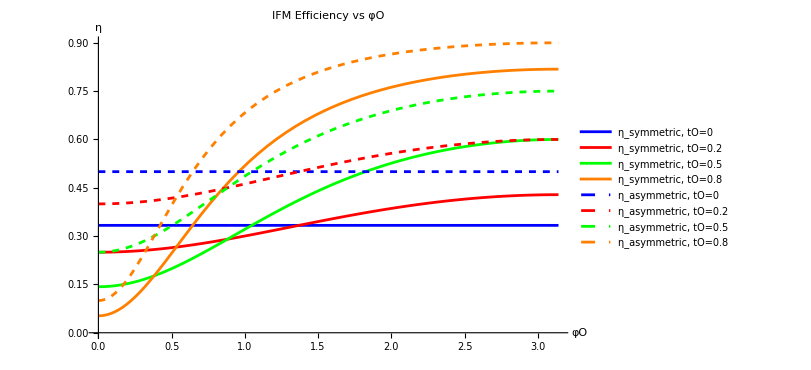

C:\Users\User\Downloads\IFM files\efficiency_plot_pase_simetrtic_with_1.pdf

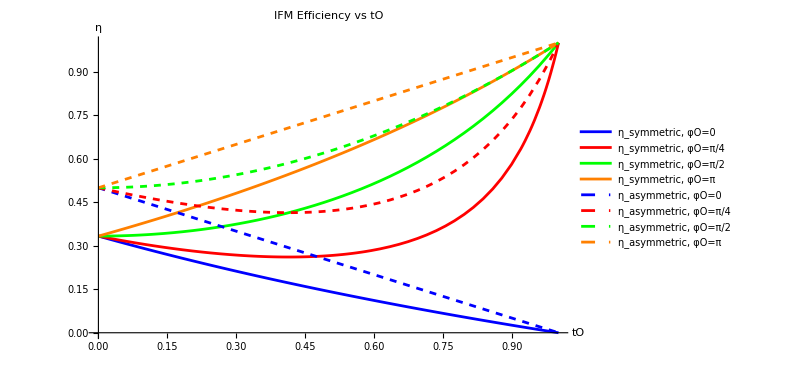

C:\Users\User\Downloads\IFM files\efficiency_plot_tO_with_1.pdf

```mathematica
graph=Labeled[Plot[Evaluate[Join[Table[η201,{tO,{0,0.2,0.5,0.8}}],Table[η110,{tO,{0,0.2,0.5,0.8}}]]],{φO,0,π},PlotLegends->Placed[{"η_symmetric, tO=0","η_symmetric, tO=0.2","η_symmetric, tO=0.5","η_symmetric, tO=0.8","η_asymmetric, tO=0","η_asymmetric, tO=0.2","η_asymmetric, tO=0.5","η_asymmetric, tO=0.8"},Automatic],PlotStyle->{{Blue},{Red},{Green},{Orange},{Blue,Dashed},{Red,Dashed},{Green,Dashed},{Orange,Dashed}},PlotLabel->Style["IFM Efficiency vs φO",16,Bold],AxesLabel->{"φO","η"},LabelStyle->{FontSize->14},ImageSize->600],Style["",13,Bold],Bottom]

Export["C:\\Users\\User\\Downloads\\IFM files\\efficiency_plot_pase_simetrtic_with_1.pdf",graph,"PDF",ImageResolution->600]

graph1=Labeled[Plot[Evaluate[Join[Table[η201,{φO,{0,π/4,π/2,π}}],Table[η110,{φO,{0,π/4,π/2,π}}]]],{tO,0,1},PlotLegends->Placed[{"η_symmetric, φO=0","η_symmetric, φO=π/4","η_symmetric, φO=π/2","η_symmetric, φO=π","η_asymmetric, φO=0","η_asymmetric, φO=π/4","η_asymmetric, φO=π/2","η_asymmetric, φO=π"},Automatic],PlotStyle->{{Blue},{Red},{Green},{Orange},{Blue,Dashed},{Red,Dashed},{Green,Dashed},{Orange,Dashed}},PlotLabel->Style["IFM Efficiency vs tO",16,Bold],AxesLabel->{"tO","η"},LabelStyle->{FontSize->14},ImageSize->600],Style["",13,Bold],Bottom]

Export["C:\\Users\\User\\Downloads\\IFM files\\efficiency_plot_tO_with_1.pdf",graph1,"PDF",ImageResolution->600]
```

### Calculation of two photon

#### input 20 probabilities w/o object asymmetric MZI

```mathematica
Probs2as[list2,2,0]
```

#### input 02 probabilities w/o object asymmetric MZI

```mathematica
Probs2as[list2,0,2]
```

#### input 11 probabilities w/o object asymmetric MZI

```mathematica
Probs2as[list2,1,1]
```

#### input 20 probabilities w/o object symmetric MZI

```mathematica
Probs2s[list2,2,0]
```

#### input 02 probabilities w/o object symmetric MZI

```mathematica
Probs2s[list2,0,2]
```

#### input 11 probabilities w/o object symmetric MZI

```mathematica
Probs2s[list2,1,1]
```

#### input 20 probabilities with object asymmetric MZI

```mathematica
Probs2obas[list2,2,0]
```

#### input 02 probabilities with object asymmetric MZI

```mathematica
Probs2obas[list2,0,2]
```

#### input 11 probabilities with object asymmetric MZI

```mathematica
Probs2obas[list2,1,1]
```

#### input 20 probabilities with object symmetric MZI

```mathematica
Probs2obs[list2,2,0]
```

#### input 02 probabilities with object symmetric MZI

```mathematica
Probs2obs[list2,0,2]
```

#### input 11 probabilities with object symmetric MZI

```mathematica
Probs2obs[list2,1,1]
```

### Calculation of IFM efficiency 2 photons

In this section we will calculate the IFM efficiency  .
Each code will describe a different dark-state, and will have different properties for the variables.
We calculate the probabiity for noticing the object with and without interaction.
The IFM efficiency is defined as : (P_(without interaction))/(P_(without interaction)+P_(with interaction))

### IFM efficiency for input 2,0 φ=0

```mathematica
(*All results as an Association*)

results20e=Probs2obas[list2,2,0];
allProbs20e=results20e["All Results"]//Normal
```

<|{0,0}→T^2 (-1+tO^2)^2,{1,0}→2 (T-T tO^2) (1-2 T+T^2 (1+tO^2)-2 (-1+T) T tO Cos[φO]),{0,1}→2 (-1+T) T^2 (-1+tO^2) (1+tO^2-2 tO Cos[φO]),{2,0}→(1-2 T+T^2 (1+tO^2)-2 (-1+T) T tO Cos[φO])^2,{0,2}→(-1+T)^2 T^2 (1+tO^2-2 tO Cos[φO])^2,{1,1}→-2 (-1+T) T (1+tO^2-2 tO Cos[φO]) (1-2 T+T^2 (1+tO^2)-2 (-1+T) T tO Cos[φO])|>

```mathematica
"IFM efficiency : "
ifme20=(allProbs20e[{0,2}]+allProbs20e[{1,1}]-allProbs20e[{0,1}]-allProbs20e[{1,0}]-allProbs20e[{0,0}])/(allProbs20e[{0,0}]+allProbs20e[{1,0}]+allProbs20e[{0,1}]+allProbs20e[{1,1}]+allProbs20e[{0,2}])//SimplifyFractionSeparate
```

IFM efficiency :

(-4 tO^2+T (4+8 tO^2-2 tO^4-4 T (1+2 tO^2)+T^2 (1+4 tO^2+tO^4))-4 (-1+T) tO (1-2 T+T^2 (1+tO^2)) Cos[φO]+2 (-1+T)^2 T tO^2 Cos[2 φO])/(-4+T (6+4 tO^2+T (-4-8 tO^2+T (1+4 tO^2+tO^4)))-4 (-1+T) tO (1-2 T+T^2 (1+tO^2)) Cos[φO]+2 (-1+T)^2 T tO^2 Cos[2 φO])

```mathematica
"optimal: "
(-4 tO^2+T (4+8 tO^2-2 tO^4-4 T (1+2 tO^2)+T^2 (1+4 tO^2+tO^4))-4 (-1+T) tO (1-2 T+T^2 (1+tO^2)) Cos[φO]+2 (-1+T)^2 T tO^2 Cos[2 φO])/(-4+T (6+4 tO^2+T (-4-8 tO^2+T (1+4 tO^2+tO^4)))-4 (-1+T) tO (1-2 T+T^2 (1+tO^2)) Cos[φO]+2 (-1+T)^2 T tO^2 Cos[2 φO])/.T->0
```

optimal:

(-4 tO^2+4 tO Cos[φO])/(-4+4 tO Cos[φO])

### IFM efficiency for input 0,2 φ=0

```mathematica
(*All results as an Association*)
results02e=Probs2obas[list2,0,2];
allProbs02e=results02e["All Results"]//Normal;
"IFM efficiency : "
ifme02=(allProbs02e[{2,0}]+allProbs02e[{1,1}]-allProbs02e[{0,1}]-allProbs02e[{1,0}]-allProbs02e[{0,0}])/(allProbs02e[{0,0}]+allProbs02e[{1,0}]+allProbs02e[{0,1}]+allProbs02e[{1,1}]+allProbs02e[{2,0}])//SimplifyFractionSeparate
```

IFM efficiency :

(-1+tO^4+T^2 (1-4 tO^2-3 tO^4)+T (-1+4 tO^2+tO^4)+T^3 (1+4 tO^2+tO^4)+T tO ((-4 T^2-4 (-1+T)^2 tO^2) Cos[φO]+2 (-1+T) T tO Cos[2 φO]))/(1+T+T^2+T^3+4 (-1+T) T^2 tO^2+(-1+T)^3 tO^4+T tO ((-4 T^2-4 (-1+T)^2 tO^2) Cos[φO]+2 (-1+T) T tO Cos[2 φO]))

```mathematica
"optimal : "
(-1+tO^4+T^2 (1-4 tO^2-3 tO^4)+T (-1+4 tO^2+tO^4)+T^3 (1+4 tO^2+tO^4)+T tO ((-4 T^2-4 (-1+T)^2 tO^2) Cos[φO]+2 (-1+T) T tO Cos[2 φO]))/(1+T+T^2+T^3+4 (-1+T) T^2 tO^2+(-1+T)^3 tO^4+T tO ((-4 T^2-4 (-1+T)^2 tO^2) Cos[φO]+2 (-1+T) T tO Cos[2 φO]))/.T->1
```

optimal :

(4 tO^2-4 tO Cos[φO])/(4-4 tO Cos[φO])

### IFM efficiency for input 1,1 φ=0

```mathematica
(*All results as an Association*)
results11e=Probs2obas[list2,1,1];
allProbs11e=results11e["All Results"]//Normal;
"IFM efficiency:"
ifme11=(allProbs11e[{0,2}]+allProbs11e[{2,0}]-allProbs11e[{0,1}]-allProbs11e[{1,0}]-allProbs11e[{0,0}])/(allProbs11e[{0,0}]+allProbs11e[{1,0}]+allProbs11e[{0,1}]+allProbs11e[{2,0}]+allProbs11e[{0,2}])//SimplifyFractionSeparate
```

IFM efficiency:

(-1+tO^2-4 (-1+T) T (1+tO^4-T (1+tO^2)^2+T^2 (1+tO^2)^2)+4 (-1+T) T tO Cos[φO] ((1-2 T)^2 (1+tO^2)-4 (-1+T) T tO Cos[φO]))/(1-tO^2+T (2.22045×10^-16+8 tO^2+8 T^2 (1+tO^2)^2-4 T^3 (1+tO^2)^2-4 T (1+4 tO^2+tO^4))+4 (-1+T) T tO Cos[φO] ((1-2 T)^2 (1+tO^2)-4 (-1+T) T tO Cos[φO]))

### IFM efficiency for input 0,2 φ=π R=T

```mathematica
(*All results as an Association*)
results02be=Probs2obs[list2,0,2];
allProbs02be=results02be["All Results"]//Normal;
ifme02b=(allProbs02be[{2,0}]+allProbs02be[{1,1}]-allProbs02be[{0,1}]-allProbs02be[{1,0}]-allProbs02be[{0,0}])/(allProbs02be[{0,0}]+allProbs02be[{1,0}]+allProbs02be[{0,1}]+allProbs02be[{1,1}]+allProbs02be[{2,0}])//SimplifyFractionSeparate
```

(9-12 tO^2-7 tO^4-4 (tO+tO^3) Cos[φO]+2 tO^2 Cos[2 φO])/(-15+4 tO^2+tO^4-4 (tO+tO^3) Cos[φO]+2 tO^2 Cos[2 φO])

### IFM efficiency for input 2,0 φ=π R=T

```mathematica
(*All results as an Association*)
results20be=Probs2obs[list2,2,0];
allProbs20be=results20be["All Results"]//Normal;
ifme20b=(allProbs20be[{2,0}]+allProbs20be[{1,1}]-allProbs20be[{0,1}]-allProbs20be[{1,0}]-allProbs20be[{0,0}])/(allProbs20be[{0,0}]+allProbs20be[{1,0}]+allProbs20be[{0,1}]+allProbs20be[{1,1}]+allProbs20be[{2,0}])//SimplifyFractionSeparate
```

(9-12 tO^2-7 tO^4+4 (tO+tO^3) Cos[φO]+2 tO^2 Cos[2 φO])/(-15+4 tO^2+tO^4+4 (tO+tO^3) Cos[φO]+2 tO^2 Cos[2 φO])

### IFM efficiency for input 1,1 φ=π R=T

```mathematica
(*All results as an Association*)
results11be=Probs2obs[list2,1,1];
allProbs11be=results11be["All Results"]//Normal;
ifme11b=(allProbs11be[{0,2}]+allProbs11be[{2,0}]-allProbs11be[{0,1}]-allProbs11be[{1,0}]-allProbs11be[{0,0}])/(allProbs11be[{0,0}]+allProbs11be[{1,0}]+allProbs11be[{0,1}]+allProbs11be[{2,0}]+allProbs11be[{0,2}])//SimplifyFractionSeparate
```

(1-3 tO^4+2 tO^2 Cos[2 φO])/(-3+tO^4+2 tO^2 Cos[2 φO])

### Dose reduction for input 2,0 φ=0

```mathematica
(*All results as an Association*)

results20=Probs2obas[list2,2,0];
allProbs20=results20["All Results"]//Normal
```

<|{0,0}→T^2 (-1+tO^2)^2,{1,0}→2 (T-T tO^2) (1-2 T+T^2 (1+tO^2)-2 (-1+T) T tO Cos[φO]),{0,1}→2 (-1+T) T^2 (-1+tO^2) (1+tO^2-2 tO Cos[φO]),{2,0}→(1-2 T+T^2 (1+tO^2)-2 (-1+T) T tO Cos[φO])^2,{0,2}→(-1+T)^2 T^2 (1+tO^2-2 tO Cos[φO])^2,{1,1}→-2 (-1+T) T (1+tO^2-2 tO Cos[φO]) (1-2 T+T^2 (1+tO^2)-2 (-1+T) T tO Cos[φO])|>

```mathematica
"Dose reduction: "
doseA20=(allProbs20[{0,2}]+allProbs20[{1,1}]-allProbs20[{0,1}]-allProbs20[{1,0}]-2*allProbs20[{0,0}])/(allProbs20[{0,0}]+allProbs20[{1,0}]+allProbs20[{0,1}]+allProbs20[{1,1}]+allProbs20[{0,2}])//SimplifyFractionSeparate
```

Dose reduction:

(-4 tO^2+T (5+6 tO^2-tO^4-4 T (1+2 tO^2)+T^2 (1+4 tO^2+tO^4))-4 (-1+T) tO (1-2 T+T^2 (1+tO^2)) Cos[φO]+2 (-1+T)^2 T tO^2 Cos[2 φO])/(-4+T (6+4 tO^2+T (-4-8 tO^2+T (1+4 tO^2+tO^4)))-4 (-1+T) tO (1-2 T+T^2 (1+tO^2)) Cos[φO]+2 (-1+T)^2 T tO^2 Cos[2 φO])

```mathematica
"optimal Dose reduction: "
(-4 tO^2+T (5+6 tO^2-tO^4-4 T (1+2 tO^2)+T^2 (1+4 tO^2+tO^4))-4 (-1+T) tO (1-2 T+T^2 (1+tO^2)) Cos[φO]+2 (-1+T)^2 T tO^2 Cos[2 φO])/(-4+T (6+4 tO^2+T (-4-8 tO^2+T (1+4 tO^2+tO^4)))-4 (-1+T) tO (1-2 T+T^2 (1+tO^2)) Cos[φO]+2 (-1+T)^2 T tO^2 Cos[2 φO])/.T->0
```

optimal Dose reduction:

(-4 tO^2+4 tO Cos[φO])/(-4+4 tO Cos[φO])

### Dose reduction for input 0,2 φ=0

```mathematica
(*All results as an Association*)
results02=Probs2obas[list2,0,2];
allProbs02=results02["All Results"]//Normal;
"Dose reduction: "
doseA02=(allProbs02[{2,0}]+allProbs02[{1,1}]-allProbs02[{0,1}]-allProbs02[{1,0}]-2*allProbs02[{0,0}])/(allProbs02[{0,0}]+allProbs02[{1,0}]+allProbs02[{0,1}]+allProbs02[{1,1}]+allProbs02[{2,0}])//SimplifyFractionSeparate
```

Dose reduction:

(-2+T^2+T^3+(2+T (2+4 (-1+T) T)) tO^2+T (2+(-3+T) T) tO^4+T tO (-4 T^2-4 (-1+T)^2 tO^2) Cos[φO]+2 (-1+T) T^2 tO^2 Cos[2 φO])/(1+T+T^2+T^3+4 (-1+T) T^2 tO^2+(-1+T)^3 tO^4+T tO ((-4 T^2-4 (-1+T)^2 tO^2) Cos[φO]+2 (-1+T) T tO Cos[2 φO]))

```mathematica
"optimal Dose reduction: "
(-2+T^2+T^3+(2+T (2+4 (-1+T) T)) tO^2+T (2+(-3+T) T) tO^4+T tO (-4 T^2-4 (-1+T)^2 tO^2) Cos[φO]+2 (-1+T) T^2 tO^2 Cos[2 φO])/(1+T+T^2+T^3+4 (-1+T) T^2 tO^2+(-1+T)^3 tO^4+T tO ((-4 T^2-4 (-1+T)^2 tO^2) Cos[φO]+2 (-1+T) T tO Cos[2 φO]))/.T->1
```

optimal Dose reduction:

(4 tO^2-4 tO Cos[φO])/(4-4 tO Cos[φO])

### Dose reduction for input 1,1 φ=0

```mathematica
(*All results as an Association*)
results11=Probs2obas[list2,1,1];
allProbs11=results11["All Results"]//Normal;
"Dose reduction:"
doseA11=(allProbs11[{0,2}]+allProbs11[{2,0}]-allProbs11[{0,1}]-allProbs11[{1,0}]-2*allProbs11[{0,0}])/(allProbs11[{0,0}]+allProbs11[{1,0}]+allProbs11[{0,1}]+allProbs11[{2,0}]+allProbs11[{0,2}])//SimplifyFractionSeparate
```

Dose reduction:

(-1+T (2+T (-6-4 (-2+T) T))+(1+T (4-4 T (3-4 T+2 T^2))) tO^2+T (2+T (-6-4 (-2+T) T)) tO^4+4 (-1+T) T tO Cos[φO] ((1-2 T)^2 (1+tO^2)-4 (-1+T) T tO Cos[φO]))/(1-tO^2+T (2.22045×10^-16+8 tO^2+8 T^2 (1+tO^2)^2-4 T^3 (1+tO^2)^2-4 T (1+4 tO^2+tO^4))+4 (-1+T) T tO Cos[φO] ((1-2 T)^2 (1+tO^2)-4 (-1+T) T tO Cos[φO]))

```mathematica
(-1+T (2+T (-6-4 (-2+T) T))+(1+T (4-4 T (3-4 T+2 T^2))) tO^2+T (2+T (-6-4 (-2+T) T)) tO^4+4 (-1+T) T tO Cos[φO] ((1-2 T)^2 (1+tO^2)-4 (-1+T) T tO Cos[φO]))/(1-tO^2+T (8 tO^2+8 T^2 (1+tO^2)^2-4 T^3 (1+tO^2)^2-4 T (1+4 tO^2+tO^4))+4 (-1+T) T tO Cos[φO] ((1-2 T)^2 (1+tO^2)-4 (-1+T) T tO Cos[φO]))
```

(-1+T (2+T (-6-4 (-2+T) T))+(1+T (4-4 T (3-4 T+2 T^2))) tO^2+T (2+T (-6-4 (-2+T) T)) tO^4+4 (-1+T) T tO Cos[φO] ((1-2 T)^2 (1+tO^2)-4 (-1+T) T tO Cos[φO]))/(1-tO^2+T (8 tO^2+8 T^2 (1+tO^2)^2-4 T^3 (1+tO^2)^2-4 T (1+4 tO^2+tO^4))+4 (-1+T) T tO Cos[φO] ((1-2 T)^2 (1+tO^2)-4 (-1+T) T tO Cos[φO]))

### Dose reduction for input 0,2 φ=π R=T

```mathematica
(*All results as an Association*)
results02b=Probs2obs[list2,0,2];
allProbs02b=results02b["All Results"]//Normal;
doseB02=(allProbs02b[{2,0}]+allProbs02b[{1,1}]-allProbs02b[{0,1}]-allProbs02b[{1,0}]-2*allProbs02b[{0,0}])/(allProbs02b[{0,0}]+allProbs02b[{1,0}]+allProbs02b[{0,1}]+allProbs02b[{1,1}]+allProbs02b[{2,0}])//SimplifyFractionSeparate
```

(13-20 tO^2-3 tO^4-4 (tO+tO^3) Cos[φO]+2 tO^2 Cos[2 φO])/(-15+4 tO^2+tO^4-4 (tO+tO^3) Cos[φO]+2 tO^2 Cos[2 φO])

### Dose reduction for input 2,0 φ=π R=T

```mathematica
(*All results as an Association*)
results20b=Probs2obs[list2,2,0];
allProbs20b=results20b["All Results"]//Normal;
doseB20=(allProbs20b[{2,0}]+allProbs20b[{1,1}]-allProbs20b[{0,1}]-allProbs20b[{1,0}]-2*allProbs20b[{0,0}])/(allProbs20b[{0,0}]+allProbs20b[{1,0}]+allProbs20b[{0,1}]+allProbs20b[{1,1}]+allProbs20b[{2,0}])//SimplifyFractionSeparate
```

(13-20 tO^2-3 tO^4+4 (tO+tO^3) Cos[φO]+2 tO^2 Cos[2 φO])/(-15+4 tO^2+tO^4+4 (tO+tO^3) Cos[φO]+2 tO^2 Cos[2 φO])

### Dose reduction for input 1,1 φ=π R=T

```mathematica
(*All results as an Association*)
results11b=Probs2obs[list2,1,1];
allProbs11b=results11b["All Results"]//Normal;
doseB11=(allProbs11b[{0,2}]+allProbs11b[{2,0}]-allProbs11b[{0,1}]-allProbs11b[{1,0}]-2*allProbs11b[{0,0}])/(allProbs11b[{0,0}]+allProbs11b[{1,0}]+allProbs11b[{0,1}]+allProbs11b[{2,0}]+allProbs11b[{0,2}])//SimplifyFractionSeparate
```

-(-3+4 tO^2+tO^4-2 tO^2 Cos[2 φO])/(-3+tO^4+2 tO^2 Cos[2 φO])

### Calculation of IFM phase sensitivity

In this section we will calculate the IFM phase sensitivity  .
sensitivity is defined as : (S^2)_φ =  (Δ^2 O)/(∂/(∂φ) <O>)^2

Sensitivity for O = N_1-N_2

```mathematica
Sens1[i_,j_,R_,T_,φ_,tO_,φO_]:=Module[{Cout,c,N,Ex,der,var,sens},
Cout=MZ[√R,√T,φ,tO,φO].ain;
c[n_]:=Cout[[n,1]];
N[m_]:=( SuperDagger[c[m]])·(c[m]);
Ex = ⟨Subscript[ψ, i,j,0]|·(N[1])·|Subscript[ψ, i,j,0]⟩-⟨Subscript[ψ, i,j,0]|·(N[2])·|Subscript[ψ, i,j,0]⟩//ComplexExpand//Simplify;
der = D[Ex,φ]//ComplexExpand//Simplify;
var = ⟨Subscript[ψ, i,j,0]|·(N[2])^2·|Subscript[ψ, i,j,0]⟩+  ⟨Subscript[ψ, i,j,0]|·(N[1])^2·|Subscript[ψ, i,j,0]⟩- 2⟨Subscript[ψ, i,j,0]|·(((N[1])·(N[2]))·|Subscript[ψ, i,j,0]⟩)-Ex^2//ComplexExpand//Simplify;

sens =var/der^2//ComplexExpand//Simplify

]


Sensitivity for O = Subscript[N, 1]
```

```mathematica
SensN1[i_,j_,R_,T_,φ_,tO_,φO_]:=Module[{Cout,c,N,Ex,der,var,sens},
Cout=MZ[√R,√T,φ,tO,φO].ain;
c[n_]:=Cout[[n,1]];
N[m_]:=( SuperDagger[c[m]])·(c[m]);
Ex = ⟨Subscript[ψ, i,j,0]|·(N[1])·|Subscript[ψ, i,j,0]⟩//ComplexExpand//Simplify;
der = D[Ex,φ]//ComplexExpand//Simplify;
var =   ⟨Subscript[ψ, i,j,0]|·(N[1])^2·|Subscript[ψ, i,j,0]⟩-Ex^2//ComplexExpand//Simplify;

sens =var/der^2//ComplexExpand//Simplify

]
Sensitivity for O = Subscript[N, 2]
SensN2[i_,j_,R_,T_,φ_,tO_,φO_]:=Module[{Cout,c,N,Ex,der,var,sens},
Cout=MZ[√R,√T,φ,tO,φO].ain;
c[n_]:=Cout[[n,1]];
N[m_]:=( SuperDagger[c[m]])·(c[m]);
Ex = ⟨Subscript[ψ, i,j,0]|·(N[2])·|Subscript[ψ, i,j,0]⟩//ComplexExpand//Simplify;
der = D[Ex,φ]//ComplexExpand//Simplify;
var =   ⟨Subscript[ψ, i,j,0]|·(N[2])^2·|Subscript[ψ, i,j,0]⟩-Ex^2//ComplexExpand//Simplify;

sens =var/der^2//ComplexExpand//Simplify

]
```

### sensitivity 10

```mathematica
Sens1[2,0,0.01,0.99,φ,tO,0]//Rationalize//Simplify
SensN1[2,0,0.01,0.99,φ,tO,0]//Rationalize//Simplify
SensN2[2,0,0.01,0.99,φ,tO,0]//Rationalize//Simplify
```

-1/(tO^2 (-1.+Cos[2 φ])^2)1200.5 Sin[φ]^2 (-0.0105217-1.07112 tO^2+tO^4+(-0.000824572 tO+0.0816327 tO^3) Cos[φ]+0.000832986 tO^2 Cos[2 φ]-(0.+1.84293×10^-18 ⅈ) tO Sin[φ])

-1/(tO^2 (-1.+Cos[2 φ])^2)4900.5 Sin[φ]^2 (-0.000104092-1.0199 tO^2+tO^4+(-0.0206081 tO+0.040404 tO^3) Cos[φ]+0.000204061 tO^2 Cos[2 φ]-(0.+5.79976×10^-18 ⅈ) tO^3 Sin[φ])

-1/(tO^2 (-1.+Cos[2 φ])^2)0.5 Sin[φ]^2 (-100.01-97.0101 tO^2+tO^4+2. tO^2 Cos[2 φ]+(0.+3.53989×10^-14 ⅈ) tO Sin[φ]-(0.+5.53108×10^-16 ⅈ) tO^3 Sin[φ]+tO Cos[φ] (198.02-4. tO^2+(0.+1.65932×10^-15 ⅈ) tO Sin[φ])+(0.+8.84973×10^-15 ⅈ) tO Sin[3 φ])

```mathematica
s10[T_,φ_,tO_]:=-1/(16 (-1+T)^2 T tO^2)(-5+13 T-12 T^2+4 T^3-3 tO^2+18 T tO^2-32 T^2 tO^2+16 T^3 tO^2+T tO^4-4 T^2 tO^4+4 T^3 tO^4-8 (1-3 T+2 T^2) tO (-1+T+T tO^2) Cos[φ]+8 (-1+T)^2 T tO^2 Cos[2 φ]) Csc[φ]^2
```

### Sensitivity 01

```mathematica
Sens1[0,1,1-T,T,φ,tO,0]
```

-((T+4 T^3+tO^2+2 T tO^2-16 T^2 tO^2+16 T^3 tO^2-tO^4+5 T tO^4-8 T^2 tO^4+4 T^3 tO^4-8 T (-1+2 T) tO (T-tO^2+T tO^2) Cos[φ]+8 (-1+T) T^2 tO^2 Cos[2 φ]) Csc[φ]^2)/(16 (-1+T) T^2 tO^2)

```mathematica
s01[T_,φ_,tO_]:=-((T+4 T^3+tO^2+2 T tO^2-16 T^2 tO^2+16 T^3 tO^2-tO^4+5 T tO^4-8 T^2 tO^4+4 T^3 tO^4-8 T (-1+2 T) tO (T-tO^2+T tO^2) Cos[φ]+8 (-1+T) T^2 tO^2 Cos[2 φ]) Csc[φ]^2)/(16 (-1+T) T^2 tO^2)
```

### Sensitivity 02

```mathematica
Sens1[0,2,1-T,T,φ,tO,0]
```

-((T+4 T^3+tO^2+2 T tO^2-16 T^2 tO^2+16 T^3 tO^2-tO^4+5 T tO^4-8 T^2 tO^4+4 T^3 tO^4-8 T (-1+2 T) tO (T-tO^2+T tO^2) Cos[φ]+8 (-1+T) T^2 tO^2 Cos[2 φ]) Csc[φ]^2)/(32 (-1+T) T^2 tO^2)

```mathematica
s02[T_,φ_,tO_]:=-1/(32 (-1+T) T^2 tO^2)(T+4 T^3+tO^2+2 T tO^2-16 T^2 tO^2+16 T^3 tO^2-tO^4+5 T tO^4-8 T^2 tO^4+4 T^3 tO^4-8 T (-1+2 T) tO (T-tO^2+T tO^2) Cos[φ]+8 (-1+T) T^2 tO^2 Cos[2 φ]) Csc[φ]^2
s02[0.999,φO,tO]
Manipulate[Plot[{s02[T,φ,1],s02[T,φ,1]},{φ,0,1}],{T,0,1}]
```

(31.3126 (4.98701+2.98203 tO^2-0.000996004 tO^4-7.97602 tO (0.999-0.001 tO^2) Cos[φO]-0.00798401 tO^2 Cos[2 φO]) Csc[φO]^2)/tO^2

### Sensitivity 20

```mathematica
Sens1[2,0,1-T,T,φ,tO,0]
```

-1/(32 (-1+T)^2 T tO^2)(-5+13 T-12 T^2+4 T^3-3 tO^2+18 T tO^2-32 T^2 tO^2+16 T^3 tO^2+T tO^4-4 T^2 tO^4+4 T^3 tO^4-8 (1-3 T+2 T^2) tO (-1+T+T tO^2) Cos[φ]+8 (-1+T)^2 T tO^2 Cos[2 φ]) Csc[φ]^2

```mathematica
s20[T_,φ_,tO_]:=-1/(32 (-1+T)^2 T tO^2)(-5+13 T-12 T^2+4 T^3-3 tO^2+18 T tO^2-32 T^2 tO^2+16 T^3 tO^2+T tO^4-4 T^2 tO^4+4 T^3 tO^4-8 (1-3 T+2 T^2) tO (-1+T+T tO^2) Cos[φ]+8 (-1+T)^2 T tO^2 Cos[2 φ]) Csc[φ]^2
s20[0.0001,φO,tO]
```

-(312.563 (-4.9987-2.9982 tO^2+0.00009996 tO^4-7.9976 tO (-0.9999+0.0001 tO^2) Cos[φO]+0.00079984 tO^2 Cos[2 φO]) Csc[φO]^2)/tO^2

### Sensitivity 11

for input 11 we look measure the coincidence operator N_1·N_2

```mathematica
Sens2[i_,j_,R_,T_,φ_,tO_,φO_]:=Module[{Cout,c,N,Ex,der,var,sens},
Cout=MZ[√R,√T,φ,tO,φO].ain;
c[n_]:=Cout[[n,1]];
N[m_]:= SuperDagger[c[m]]·c[m];
Ex = ⟨Subscript[ψ, i,j,0]|·(N[1])·(N[2])·|Subscript[ψ, i,j,0]⟩//ComplexExpand//Simplify;
der = D[Ex,φ]//ComplexExpand//Simplify;
var =⟨Subscript[ψ, i,j,0]|·((N[1])·(N[2]))^2·|Subscript[ψ, i,j,0]⟩-Ex^2//ComplexExpand//Simplify;

sens =var/der^2//ComplexExpand//Simplify

]
Sens2[1,1,1-T,T,φ,tO,0]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of the TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

```mathematica
s11[T_,tO_,φ_]:=-(((-4 T^2+8 T^3+12 T^4-64 T^5+96 T^6-64 T^7+16 T^8-tO^2+8 T tO^2-8 T^2 tO^2-128 T^3 tO^2+640 T^4 tO^2-1408 T^5 tO^2+1664 T^6 tO^2-1024 T^7 tO^2+256 T^8 tO^2+tO^4-16 T tO^4+124 T^2 tO^4-600 T^3 tO^4+1836 T^4 tO^4-3456 T^5 tO^4+3840 T^6 tO^4-2304 T^7 tO^4+576 T^8 tO^4+16 T^2 tO^6-160 T^3 tO^6+656 T^4 tO^6-1408 T^5 tO^6+1664 T^6 tO^6-1024 T^7 tO^6+256 T^8 tO^6+16 T^4 tO^8-64 T^5 tO^8+96 T^6 tO^8-64 T^7 tO^8+16 T^8 tO^8-4 (1-2 T)^2 (-1+T) T tO (1+tO^2) (-1+2 tO^2-16 T tO^2-16 T^3 (1+5 tO^2+tO^4)+8 T^4 (1+5 tO^2+tO^4)+8 T^2 (1+7 tO^2+tO^4)) Cos[φ]+8 (-1+T)^2 T^2 tO^2 (tO^2 (4+tO^2)+32 T^2 (1+3 tO^2+tO^4)-8 T (1+4 tO^2+tO^4)-16 T^3 (3+8 tO^2+3 tO^4)+8 T^4 (3+8 tO^2+3 tO^4)) Cos[2 φ]+32 T^3 tO^3 Cos[3 φ]-224 T^4 tO^3 Cos[3 φ]+608 T^5 tO^3 Cos[3 φ]-800 T^6 tO^3 Cos[3 φ]+512 T^7 tO^3 Cos[3 φ]-128 T^8 tO^3 Cos[3 φ]+32 T^3 tO^5 Cos[3 φ]-224 T^4 tO^5 Cos[3 φ]+608 T^5 tO^5 Cos[3 φ]-800 T^6 tO^5 Cos[3 φ]+512 T^7 tO^5 Cos[3 φ]-128 T^8 tO^5 Cos[3 φ]+32 T^4 tO^4 Cos[4 φ]-128 T^5 tO^4 Cos[4 φ]+192 T^6 tO^4 Cos[4 φ]-128 T^7 tO^4 Cos[4 φ]+32 T^8 tO^4 Cos[4 φ]) Csc[φ]^2)/(16 (-1+T)^2 T^2 tO^2 ((1-2 T)^2 (1+tO^2)-8 (-1+T) T tO Cos[φ])^2))
s11[1/2,tO,φ]
```

-((-3/16+tO^8/16+1/2 tO^2 (tO^2 (4+tO^2)+8 (1+3 tO^2+tO^4)-4 (1+4 tO^2+tO^4)-3/2 (3+8 tO^2+3 tO^4)) Cos[2 φ]+1/8 tO^4 Cos[4 φ]) Csc[φ]^2 Sec[φ]^2)/(4 tO^4)